## PID tune: explore PID tuning rules.... (Problem 3.22)

```mathematica
Clear["Global`*"];
```

Define Sample process and step response

```mathematica
tmax=100;
g0=Exp[-s]/(10 s+1)^2;g0tf=TransferFunctionModel[g0,s];
y0out=OutputResponse[g0tf,1,{t,0,tmax}];
```

Simple proportional feedback (adjust to find critical gain, kp ~ 20.67, Tc ~ 14.2)

{ⅇ^-s/(1+10 s)^2,20.67TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1120.6711FalseFalseFalseAutomaticNoneAutomatic,(20.67 ⅇ^-s)/(1.+20. s+100. s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1120.671.1FalseFalseFalseAutomaticNoneNoneAutomatic,(20.67 ⅇ^(-1. s))/(1.+20.67 ⅇ^(-1. s)+20. s+100. s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1120.671.1FalseFalseFalseAutomaticNoneNoneAutomatic}

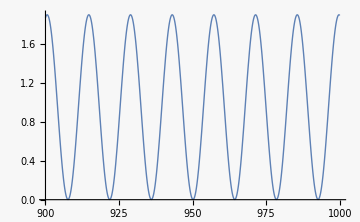

```mathematica
k0=TransferFunctionModel[20.67,s];
L0=SystemsModelSeriesConnect[g0tf,k0];
c0=SystemsModelFeedbackConnect[L0];
y0=OutputResponse[c0,1,{t,0,1000}];
{g0,k0,L0,c0} 
Plot[y0,{t,900,1000},PlotRange->All]
```

```mathematica
N[(490.4-305.8)/13]
```

14.2

Relay feedback:  Kc ~19.2  , Tc ~ 14.9

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

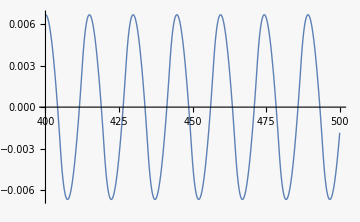

```mathematica
sol=NDSolve[{100y''[t]+20 y'[t]+y[t] ==-0.1Sign[y[t-1]],y[0]==0.06,y'[0]==0},y,{t,0,500}];
Plot[y[t]/.sol,{t,400,500},ImageSize->Medium]
```

```mathematica
{(* Kc *) N[(4/π)/0.06627],(* Tc *) N[(475-103.3)/25]}
(* need 4/π factor to get amplitude of square wave 1st harmonic *)
```

{19.2129,14.868}

my best “tweaking” effort to find PIDF algorithm  (needs a large input range)

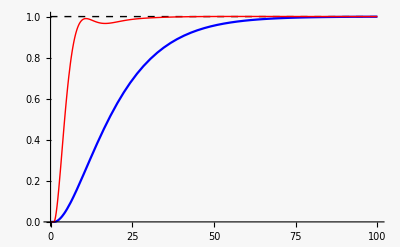
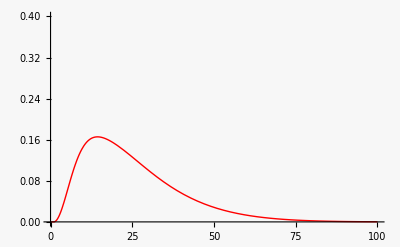
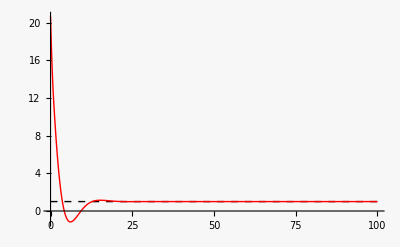

```mathematica
k1=4+0.2/s+(20s)/(1.2s+1);
k1tf=TransferFunctionModel[k1,s];
t1=(k1 g0)/(1+k1 g0); t1tf=TransferFunctionModel[t1,s]; (* command response *)
u1=k1/(1+k1 g0); u1tf=TransferFunctionModel[u1,s]; (* system input *)
d1=g0/(1+k1 g0); d1tf=TransferFunctionModel[d1,s]; (* disturbance response *)
y1out=OutputResponse[t1tf,1,{t,0,tmax}];
u1out=OutputResponse[u1tf,1,{t,0,tmax}];
d1out=OutputResponse[d1tf,1,{t,0,tmax}];
{Plot[{1,y0out,y1out},{t,0,tmax},PlotRange->All,PlotStyle->{{Dashed,Black,Thin},Blue,{Thick,Red}}],
Plot[d1out,{t,0,tmax},PlotRange->{0,0.4},PlotStyle->{{Thick,Red}}],
Plot[{1,u1out},{t,0,tmax},PlotRange->All,PlotStyle->{{Dashed,Black,Thin},{Thick,Red}}]}
```

optimized PI algorithm (from ZN knowing system, but my optimum is similar)

```mathematica
k2tf=PIDTune[g0tf,{"PI","ZieglerNichols"}];
k2tf//N//Simplify
```

(0.0811897+1.85596 s)/sTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s110.08118970769096807$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

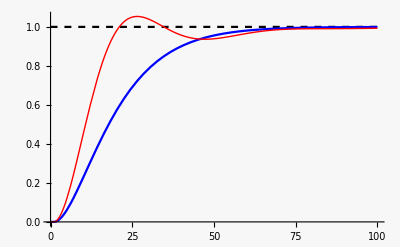
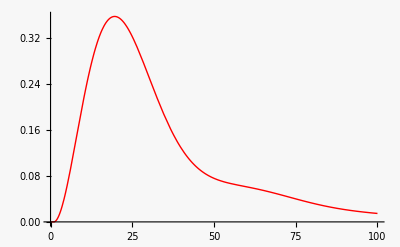
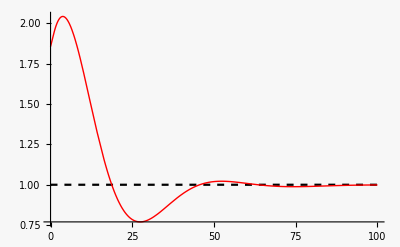

```mathematica
k2=(0.08118970769096807+1.8559600136452905 s)/s;
t2=(k2 g0)/(1+k2 g0); t2tf=TransferFunctionModel[t2,s]; (* command response *)
u2=k2/(1+k2 g0); u2tf=TransferFunctionModel[u2,s]; (* system input *)
d2=g0/(1+k2 g0); d2tf=TransferFunctionModel[d2,s]; (* disturbance response *)
y2out=OutputResponse[t2tf,1,{t,0,tmax}];
u2out=OutputResponse[u2tf,1,{t,0,tmax}];
d2out=OutputResponse[d2tf,1,{t,0,tmax}];
{Plot[{1,y0out,y2out},{t,0,tmax},PlotRange->All,PlotStyle->{{Dashed,Black},Blue,{Thick,Red}}],
Plot[d2out,{t,0,tmax},PlotStyle->{{Thick,Red}}],Plot[{1,u2out},{t,0,tmax},PlotRange->All,PlotStyle->{{Dashed,Black},{Thick,Red}}]}
```

Ziegler-Nichols PI algorithm

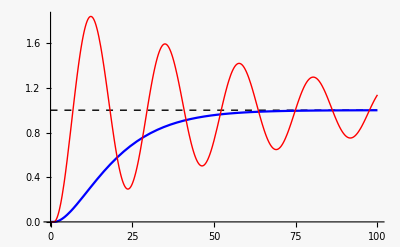
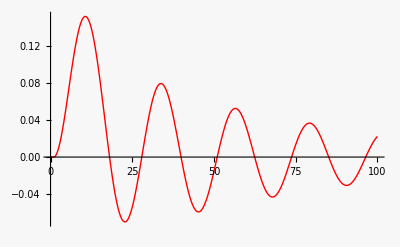
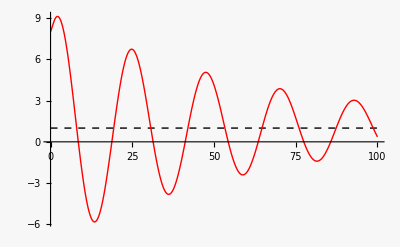

```mathematica
k3=8(1+1/((0.8*14)s)); (* ZN based on Kc=20 and Tc=14 *)
t3=(k3 g0)/(1+k3 g0); t3tf=TransferFunctionModel[t3,s]; (* command response *)
u3=k3/(1+k3 g0); u3tf=TransferFunctionModel[u3,s]; (* system input *)
d3=g0/(1+k3 g0); d3tf=TransferFunctionModel[d3,s]; (* disturbance response *)
y3out=OutputResponse[t3tf,1,{t,0,tmax}];
u3out=OutputResponse[u3tf,1,{t,0,tmax}];
d3out=OutputResponse[d3tf,1,{t,0,tmax}];
{Plot[{1,y0out,y3out},{t,0,tmax},PlotRange->All,PlotStyle->{{Dashed,Black,Thin},Blue,{Thick,Red}}],
Plot[d3out,{t,0,tmax},PlotStyle->{{Thick,Red}}],Plot[{1,u3out},{t,0,tmax},PlotRange->All,PlotStyle->{{Dashed,Black,Thin},{Thick,Red}}]}
```

```mathematica
{N[.8*14],N[8/.8/14]}
```

{11.2,0.714286}

Export data

```mathematica
dt=0.1;
dat=Table[{t,y0out[[1]],y1out[[1]],u1out[[1]],d1out[[1]],y2out[[1]],u2out[[1]],d2out[[1]],y3out[[1]],u3out[[1]],d3out[[1]]},{t,0,tmax,dt}];
(* 
SetDirectory[NotebookDirectory[]];
Export["PIDtune_out.dat", dat]; 
*)
```